```mathematica
Integrate[Integrate[Integrate[Exp[r^3] r^2 Sin[p],{r,0,1}],{t,0,2Pi}],{p,0,Pi}]
```

4/3 (-1+ⅇ) π

```mathematica
2*Integrate[Integrate[Integrate[Exp[r^3] r^2 Sin[p],{r,0,1}],{t,0,Pi}],{p,0,Pi}]
```

4/3 (-1+ⅇ) π

```mathematica
Integrate[Integrate[Integrate[r^2 Sin[p],{r,0,Cos[p]}],{t,0,2Pi}],{p,0,Pi/4}]
```

π/8

```mathematica
2*Integrate[Integrate[r Sqrt[16-r^2],{r,0,2}],{t,0,2Pi}]//N
```

93.9578

```mathematica
4Pi(64-12^(3/2))/3//N
```

93.9578

```mathematica
ContourPlot3D[{x^2+y^2==4,4x^2+4y^2+z^2==64,z==0},{x,-5,5},{y,-5,5},{z,-10,10}]
```

-Graphics3D-

```mathematica
8Pi(64-24 Sqrt[3])/3//N
```

187.916

```mathematica
f[x_,y_]:=(Sin[2x+y])^2
```

```mathematica
D[f[x,y],x]
D[f[x,y],y]
D[f[x,y],{x,2}]
D[f[x,y],x,y]
D[f[x,y],{y,2}]
```

4 Cos[2 x+y] Sin[2 x+y]

2 Cos[2 x+y] Sin[2 x+y]

8 Cos[2 x+y]^2-8 Sin[2 x+y]^2

4 Cos[2 x+y]^2-4 Sin[2 x+y]^2

2 Cos[2 x+y]^2-2 Sin[2 x+y]^2

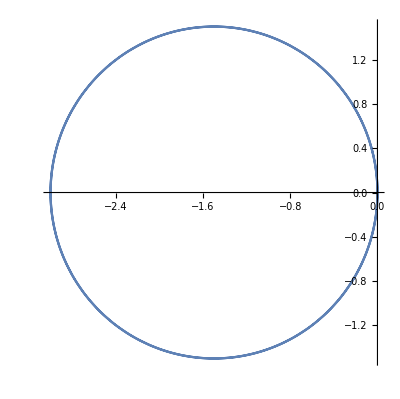

```mathematica
ParametricPlot[-3Cos[t],{t,0,2Pi}]
```

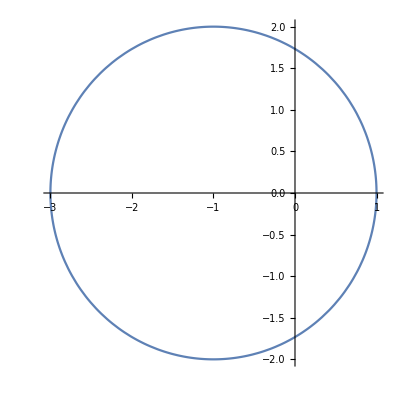

```mathematica
PolarPlot[{-Cos[t]+Sqrt[Cos[t]^2+3]},{t,0,2Pi}]
```

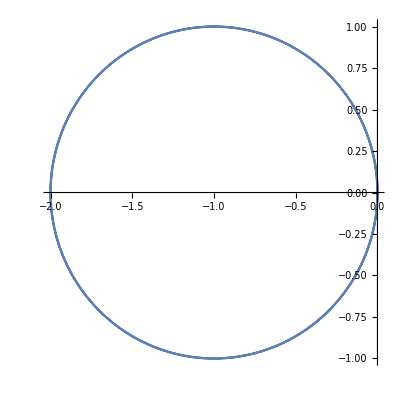

```mathematica
PolarPlot[-2Cos[t],{t,0,2Pi}]
```

```mathematica
ContourPlot3D[{y^2+z^2==4,x==2y},{x,-1,5},{y,-1,1},{z,-1,5},AspectRatio->1/1]
```

-Graphics3D-

```mathematica
?AspectRatio
```

AspectRatio is an option for Graphics and related functions that specifies the ratio of height to width for a plot.

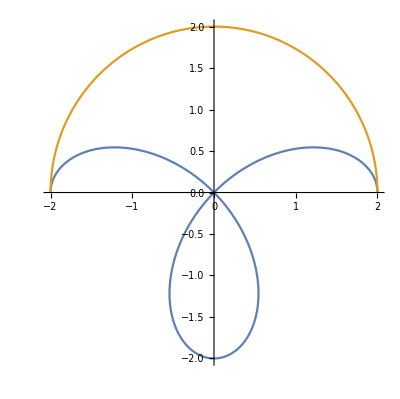

```mathematica
PolarPlot[{2Cos[2t],2},{t,0,Pi}]
```

```mathematica
ContourPlot3D[x+y+z==2,{x,0,3},{y,0,3},{z,0,3}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[Exp[y/x],{y,2x^2,3-x^2}],{y,-5,5}]
```

10 ⅇ^-x (ⅇ^(3/x)-ⅇ^(3 x)) x

```mathematica
Integrate[Integrate[r Exp[Tan[t]],r],t]
```

-1/4 ⅈ ⅇ^-ⅈ r^2 (ⅇ^(2 ⅈ) ExpIntegralEi[-ⅈ+Tan[t]]-ExpIntegralEi[ⅈ+Tan[t]])

```mathematica
Integrate[Integrate[Exp[x^2+y^2],{y,Sqrt[1-x^2],Sqrt[4-x^2]}],{x,0,1}]
```

∫_0^1 1/2 ⅇ^(x^2) √π (-Erfi[√(1-x^2)]+Erfi[√(4-x^2)])ⅆx

```mathematica
Integrate[Integrate[r Exp[r^2],{r,0,3}],{t,0,2Pi}]//N
```

25453.4

```mathematica
Integrate[Integrate[Exp[x^2+y^2],{x,-Sqrt[9-y^2],Sqrt[9-y^2]}],{y,-3,3}]//N
```

25453.4

```mathematica
Integrate[Integrate[x^2+y^2,{y,x^2,2x}],{x,0,2}]
```

216/35

```mathematica
Integrate[Integrate[x^2+y^2,{x,y/2,Sqrt[y]}],{y,0,4}]
```

216/35

```mathematica
Plot3D[x y,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[x y,{y,1,-2/5x+17/5}],{x,1,6}]
```

125/6

```mathematica
Integrate[Integrate[x y,{x,1,-5/2(y-17/5)}],{y,1,3}]
```

125/6

```mathematica
2Integrate[Integrate[r Sqrt[9-r^2],{r,Sqrt[3],3}],{t,0,2Pi}]
```

8 √6 π

```mathematica
2Integrate[Integrate[r Sqrt[9-r^2],{t,0,2Pi}],{r,Sqrt[3],3}]
```

8 √6 π

```mathematica
Integrate[Integrate[r Sqrt[1+4r^2],{r,Sqrt[7],Sqrt[12]}],{t,0,2Pi}]
```

1/6 (343-29 √29) π

```mathematica
Integrate[Integrate[Integrate[6 x y,{z,0,1+x+y}],{y,0,Sqrt[x]}],{x,0,1}]
```

65/28

```mathematica
Integrate[Integrate[Integrate[1,{y,-1,4-z}],{z,-Sqrt[4-x^2],Sqrt[4-x^2]}],{x,-2,2}]
```

20 π

```mathematica
Integrate[Integrate[Integrate[r,{y,-1,4-r Cos[t]}],{r,0,2}],{t,0,2Pi}]
```

20 π

```mathematica
Integrate[Integrate[Integrate[(r Cos[t]+r Sin[t]+z)r,{z,0,4-r^2}],{r,0,2}],{t,0,2Pi}]
```

(32 π)/3

```mathematica
Integrate[Integrate[Integrate[(9-(r Sin[p] Cos[t])^2-(r Sin[p] Sin[t])^2)(r^2 Sin[p]),{r,0,3}],{t,0,2Pi}],{p,0,Pi/2}]
```

(486 π)/5

```mathematica
Integrate[Integrate[Integrate[1,{z,0,2-x-y}],{y,0,2-x}],{x,0,2}]
```

4/3